# SurfCalc for OGP CCD in-jig measurement data.

PZ Takacs

## SurfCalc OGP_MF03 commission.nb

## Extracted from SurfAnal10b

2014.12.12 - from SurfCalc OGP_CCDonMF01 ver4.nb. Customized for commissioning the MF03 holddown fixture. Added ball sphere fitting section.

```mathematica
Button["Run Initialization first",FrontEndExecute[FrontEndToken["EvaluateInitialization"]]]
```

Run Initialization first

## 1. Initialize

Data and time of last saved modification. This is an Initialization cell that executes automatically whenever the nb is opened.

```mathematica
nb=EvaluationNotebook[]
```

vs42k_shm16FrontEndObject[LinkObject["vs42k_shm", 3, 1]]16SurfCalc OGP_MF03 commission.nb/Users/takacs/ Peter work f/Projects/LSST project/Analysis codes/SurfCalc OGP_MF03 commission.nb

```mathematica
DateString["FileModificationTime"/.NotebookInformation[],TimeZone->0]
```

Mon 5 Jan 2015 19:17:52

```mathematica
hms$:=DateString[{"Hour","Minute","Second"}]
```

```mathematica
Off[General::"spell1"]
```

```mathematica
<<ComputationalGeometry`
```

```mathematica
$SystemID
```

MacOSX-x86-64

```mathematica
$OperatingSystem
```

MacOSX

```mathematica
TS[x_]:=ToString[x]
```

#### Conversion factors to meters for numbers in the indicated units:

```mathematica
mm=10.^-3;
micron=10.^-6;
µm=10.^-6;
nm=10.^-9;
Angstroms=10.^-10;
micronsToAngstroms=10^4;
```

## 1.1. Define statistical functions for profile data. (Inactive)

```mathematica
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}]
```

MAKE SURE THE FOURIER OPTIONS ARE SET CORRECTLY EACH TIME THE FT IS DONE.

Define the biased stddev functiion. The built in StdDev fcn has n-1 in the denom. Change it to n.

Now compute std dev in different ways: The default StandardDeviation is the unbiased version, with n-1 in the denominator.

```mathematica
sdevBiased=.
```

```mathematica
sdevUnB[in_]:=N[StandardDeviation[in]]
```

```mathematica
sdevBiased[in_]:=StandardDeviation[in]Sqrt[(Length[in]-1)/Length[in]]
```

```mathematica
rmsBias[in_]:=Sqrt[Plus@@(in^2)/Length[in]]
```

Next is the RMS. Sum the squares, divide by N and then take the root. (Root of the Mean Square)

```mathematica
rmsrawbiased=.;
```

```mathematica
rms[in_]:=N[√((Plus@@((in)^2))/Length[in])]
```

See that one must subtract the mean from the input data first, before squaring, in order to compute the standard deviation correctly.

```mathematica
sdevBruteUnBiased[in_]:=N[√((Plus@@((in-Mean[in])^2))/(Length[in]-1))]
```

```mathematica
detrend[anylist_,order_Integer]:=Block[{npts,xlist,fitlist,x},
If[
order>=0,
xlist=Table[x^i,{i,0,order}];
		npts=Length[anylist];
		func=Fit[anylist,xlist,x];
		fitlist={};
		Do[AppendTo[fitlist,func],{x,1,npts}];
		Return[anylist-fitlist],
Return[anylist]
]
]
```

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list.

```mathematica
psd1[in_,delx_]:=(SetOptions[Fourier,FourierParameters->{1,1}];
nPts=Length[in];
FTwork=Fourier[in];
psd2side=(2 delx/nPts) Abs[FTwork]^2;
psd1side=Drop[psd2side,-Floor[(nPts-1)/2]];
(*Apply bookkeeping factors to end terms*)
psd1side[[1]]=psd1side[[1]]/2; 
If[EvenQ[nPts],psd1side[[-1]]=psd1side[[-1]]/2,Null];
psd1side
)
```

```mathematica
npts=.
```

```mathematica
test11={1,2,3,4,5,6,7,8,9,10,11};
```

```mathematica
psd1[test11,1.]
```

{396.,69.2929,18.8168,9.62957,6.64709,5.6137}

```mathematica
nPts
```

11

```mathematica
Length[psd2side]
```

11

#### Define a RMS function to compute rms from PSD data. Input arguments are: psd=name of PSD list; ntot=total points in source profile; delx= physical increment value for each data point step; lo and hi = index value in the PSD list. NOTE: Need to know the length of the input z-vector for the ntot number. Can't get it from the length of the psd list. It should be the length of the psd2side list if this corresponds to the input psd list.

```mathematica
rmspsdIDX[psd_,nztot_,delx_,lo_,hi_]:=(rmsval=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];Print["RMS over index range [",lo,",",hi,"] = ",rmsval])
```

```mathematica
rmspsd[psd_,nztot_,delx_,lo_,hi_]:=N[√((Plus@@Take[psd,{lo,hi}])/(nztot delx))];
```

Now generalize the variance calculation to apply to zero-padded data to give the same result as for the original data set. Need to boost up each term separately.

```mathematica
varGen[anylist_,beforeLen_,afterLen_]:=N[sfac=afterLen/beforeLen;(sfac Plus@@(anylist^2))/afterLen-sfac^2 ((Plus@@anylist)/afterLen)^2]
```

```mathematica
sdevGen=√varGen[worklist,nbefore,nafter]
```

√(-(1. worklist^2)/nbefore^2+(2.+worklist)/nbefore)

#### Add a point digitizer to a plot. Results are put into vector "res".

```mathematica
locatePts[plotname_]:=
Block[ {}, 
res = {}; 
Dynamic[res]; 
  EventHandler[ 
         plotname, {"MouseDown" :>( AppendTo[res, MousePosition["Graphics"]])} 
        ] ]
```

#### The following tick function rescales the axes labels from the default [xmin, xmax] range by offsetting the starting point by b and scaling the tick value by m. Note that you need to specify the AxesOrigin in terms of the unshifted function.

```mathematica
$TextStyle={FontFamily->Arial,FontSize->10}
```

{FontFamily→Arial,FontSize→10}

```mathematica
Style[PlotLabel,DefaultOptions->{FontFamily->Arial}]
```

PlotLabel

```mathematica
tickf[min_,max_,m_,b_,step_]:= Table[{i,m (i-b)},{i,min,max,step}]
```

File name conventions

```mathematica
filename=.;filenamefull=.;fnames=.;plotname=.;filepath=.;filepathfull=.;
```

```mathematica
filein=.;fileinroot=.;fileinS=.;
```

## 2. Enter full file path here to set working directory:

Enter the filepath for a file in each of the data directories, then copy the desired path into the filepathfull expression.

#### OGP in-jig metrology file paths

```mathematica
"/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work/MF03 141212 ballsand surfs.DAT"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work/MF03 141212 ballsand surfs.DAT

#### Execute following after setting the proper file path.

```mathematica
filepathfull = "/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work/MF03 141212 ballsand surfs.DAT";
```

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work

Use the filename form appropriate for the computer platform, either MacOSX or Windows

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[$OperatingSystem=="Windows",sep$="\\",sep$="/"];
```

```mathematica
manualcalcFlag=False; (*set for automated analysis*)
```

```mathematica
manualcalcFlag=True; (*to stop automated analysis with default parameters*)
```

## 2.1 Ball locations from OGP printout. Global coords where x-y origin is from the initialization results.

```mathematica
fitbasis={1,x,y};fitidx="1,1";
fitord$=StringTake[ToString[fitbasis],{2,-2}]
```

1, x, y

```mathematica
ballLL={109.68021,47.37074,-29.36903,8.03260/2};ballLR={196.16174,46.89109,-29.39688,8.02161/2};
ballUC={153.62359,160.61988,-29.35125,8.01668/2};
```

```mathematica
(* for 141231 data *)
ballLL={14.37264,41.5273,-29.40122,4.00253};ballLR={100.87930,41.62255,-29.37040,3.92891};
ballUC={57.49383,155.05464,-029.51954,4.13259};
```

```mathematica
ballcenters=.;
```

```mathematica
ballCentOGP=.;
```

```mathematica
ballsOGPMM={ballLL,ballLR,ballUC}
```

{{14.3726,41.5273,-29.4012,4.00253},{100.879,41.6226,-29.3704,3.92891},{57.4938,155.055,-29.5195,4.13259}}

```mathematica
Drop[ballsOGPMM,None,-1]
```

{{14.3726,41.5273,-29.4012},{100.879,41.6226,-29.3704},{57.4938,155.055,-29.5195}}

```mathematica
balldatumplaneOGP[x_,y_]=Fit[Drop[ballsOGPMM,None,-1],fitbasis,{x,y}]
```

-29.3574+0.00035757 x-0.00117803 y

## 3. Read in OGP txt format. Contours. This is treated as FREEFORM data, i.e. no set nrows or ncols.

Data is in the form of a big list of triplets in units of mm. The X,Y coordinate is included with the z-value. Note that this is NOT a rectangular data array, so can't use the array plot functions unless the data is padded to make a grid, which is not possible with OGP freefom data.

```mathematica
SetDirectory[DirectoryName[filepathfull]]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work

```mathematica
datain=.;datain2=.;datainXYZSR=.;skipnum=.;nRows=.;nCols=.;delx=.; dely=.;(*nominal scan values *)
```

```mathematica
fnames=FileNames["*.DAT"];Table[{i,fnames[[i]]},{i,Length[fnames]}]//TableForm
```

1 | MF03 141212 ballsand surfs.DAT
2 | MF03 141230a balls and surfs2.DAT
3 | MF03 141230 balls and surfs2.DAT
4 | MF03 141230 balls and surfs.DAT
5 | MF03_141231_cal01.DAT
6 | MF03_141231_cal02.DAT
7 | MF03_141231_cal03.DAT
8 | MF03_141231_cal04.DAT
9 | MF03_141231_cal05.DAT
10 | test 3balls.DAT

#### Pick the OGP file from the list

```mathematica
inst$="OGP"
```

OGP

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
nf=Input["Enter index of file desired",nf]
```

9

```mathematica
fileinfull =fnames[[nf]]
fileinroot=FileBaseName[fileinfull]
fileinS=fileinroot;filein=fileinS;
```

MF03_141231_cal05.DAT

MF03_141231_cal05

```mathematica
(*Read in raw data here*)
datain=Import[fileinfull,"Data"];
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ](* Stop here to execute next expressons individually as needed to clean up data *)
```

```mathematica
datain[[1;;20]]
```

{{C:\DATA\MF03,holddown\MF03,cal,with,scribe,marks.RTN,12/31/2014,16:50:06,2},{Point,1},{0.317571,-0.235426,-0.002881,mm},{},{Point,2},{44.0277,-5.25466,-0.019882,mm},{},{Contour,3},{44.022,-4.99528,-0.020051,mm},{44.222,-4.99407,-0.019927,mm},{44.422,-4.99286,-0.020073,mm},{44.622,-4.99162,-0.020232,mm},{44.822,-4.99038,-0.020292,mm},{45.022,-4.98914,-0.020382,mm},{45.222,-4.98788,-0.020439,mm},{45.422,-4.98664,-0.020568,mm},{45.622,-4.98537,-0.020678,mm},{45.822,-4.98409,-0.020611,mm},{46.022,-4.98284,-0.020715,mm},{46.222,-4.98156,-0.020895,mm}}

Create subdir for data file output

```mathematica
Directory[]  (* This is the current default directory *)
workdir=filein<>"_files"
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work

MF03_141231_cal05_files

```mathematica
If[!DirectoryQ[workdir],CreateDirectory[workdir];Print["New work dir created"],Print[workdir<>" already exists. Using it for output."]]
```

MF03_141231_cal05_files already exists. Using it for output.

```mathematica
SetDirectory[workdir]
```

/Users/takacs/ Peter work f/Projects/LSST project/DATA_LSST/MF03 holddown/3ball work/MF03_141231_cal05_files

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Strip out all of the Contour record, nulls and EORs, making one long list of points.

```mathematica
Length[datain]
Count[datain,{}] (* Counts the number of blank records in the file*)
```

7039

64

```mathematica
datain2=Select[datain,Length[#]>0&];(*Strip out the blank lines*)
```

```mathematica
contourPos=Position[datain2,"Contour",2]
Length[contourPos]
```

{{6,1},{196,1},{386,1},{576,1},{766,1},{956,1},{1146,1},{1336,1},{1526,1},{1716,1},{1893,1},{2083,1},{2273,1},{2463,1},{2653,1},{2845,1},{3012,1},{3179,1},{3346,1},{3513,1},{3680,1},{3847,1},{4014,1},{4181,1},{4348,1},{4515,1},{4682,1},{4849,1},{5016,1},{5183,1},{5352,1},{5401,1},{5453,1},{5501,1},{5563,1},{5625,1},{5687,1},{5745,1},{5808,1},{5867,1},{5932,1},{6003,1},{6078,1},{6144,1},{6210,1},{6273,1},{6345,1},{6408,1},{6477,1},{6583,1},{6651,1},{6718,1},{6782,1},{6847,1},{6879,1}}

55

Delete all of the Point points. Find all the locations where Point occurs. Form ppos2 by taking each positin and adding 1 to specify the data point values corresponding to the Point function. THen Delete the point pairs.

```mathematica
pointPos=Position[datain2,"Point",2]
Length[pointPos]
```

{{2,1},{4,1},{2843,1},{5350,1},{6076,1},{6581,1}}

6

```mathematica
ppos=Take[pointPos,All,1]
```

{{2},{4},{2843},{5350},{6076},{6581}}

```mathematica
ppos2=Table[{ppos[[i]],ppos[[i]]+1},{i,Length[ppos]}]//Flatten[#,1]&
```

{{2},{3},{4},{5},{2843},{2844},{5350},{5351},{6076},{6077},{6581},{6582}}

```mathematica
Length[datain2]
```

6975

```mathematica
datain2=Delete[datain2,ppos2];
```

```mathematica
ppos2={};(*Reset the list to blank after the Delete to avoid excess deletion for subsequent pass troughs*)
```

```mathematica
Length[datain2]
```

6963

Remove all of the data points defined by the “Point” identifier.

```mathematica
Length[datain2]
datain2=Select[datain2,NumericQ[#[[1]]]&]; (* Strip out all the lines that don't start with a number *)
Length[datain2]
```

6963

6903

```mathematica
datain2[[1;;10]]//TableForm
```

44.022 | -4.99528 | -0.020051 | mm
44.222 | -4.99407 | -0.019927 | mm
44.422 | -4.99286 | -0.020073 | mm
44.622 | -4.99162 | -0.020232 | mm
44.822 | -4.99038 | -0.020292 | mm
45.022 | -4.98914 | -0.020382 | mm
45.222 | -4.98788 | -0.020439 | mm
45.422 | -4.98664 | -0.020568 | mm
45.622 | -4.98537 | -0.020678 | mm
45.822 | -4.98409 | -0.020611 | mm

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Interrupt[] ]
```

#### All data points are now in one continuous list. All the contours are merged together

#### continue here

```mathematica
datain3x=Take[datain2,All,3];(* Strip off the XYZ numbers*)
```

Convert z-vals to microns:

```mathematica
xunit$="mm";yunit$="mm";(*These are now current units*)
```

```mathematica
zflag=Input["True if leave z-vals in mm",True]
```

True

```mathematica
datain3x[[1]]
If[zflag,zunit$="mm",datain3x=Map[MapAt[Times[#,10^3]&,#,3]&,datain3x];zunit$="µm"];
datain3x[[1]]
```

{44.022,-4.99528,-0.020051}

{44.022,-4.99528,-0.020051}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
datainXYZS=datain3x;
datainXYZSR=datainXYZS; (* No FID. Copy surface into SR array. *)
```

```mathematica
skipnum=.;cloudXYZ=.
```

```mathematica
cloudXYZ=datainXYZSR;
Dimensions[cloudXYZ]
```

{6903,3}

Range of raw z-values:

```mathematica
{Min[cloudXYZ[[All,{3}]]],Max[cloudXYZ[[All,{3}]]]}
```

{-27.4709,0.021036}

### Plot free-form data list not on uniform grid

#### Start next range clean-up here. Keep eliminating points from cloudXYZ based on x and y and z range criteria.

Execute the appropriate unpacking expression and rearrange the cloudXYZ as necessary.
This depends on the ordering of the XYZ values in each triplet:  XYZ or ZYX

```mathematica
xvals=Take[cloudXYZ,All,{1}]//Flatten;
yvals=Take[cloudXYZ,All,{2}]//Flatten;
zvals=Take[cloudXYZ,All,{3}]//Flatten;
```

```mathematica
{xmin=Min[xvals],xmax=Max[xvals]}//N
{ymin=Min[yvals],ymax=Max[yvals]}//N
{zmin=Min[zvals],zmax=Max[zvals],Mean[zvals],StandardDeviation[zvals]}//N
```

{10.6746,103.246}

{-4.99528,199.507}

{-27.4709,0.021036,-5.95973,10.8738}

```mathematica
{deltaX=xmax-xmin, deltaY=ymax-ymin,deltaZ=zmax-zmin}
```

{92.571,204.503,27.492}

```mathematica
rowscols$="cloud" (*"sparse"*)
```

cloud

Next expression may not contain desired array on first pass. Why???? BEWARE

```mathematica
vp={0,0,Infinity};
Dynamic[vp];
```

```mathematica
Dimensions[cloudXYZ]
```

{6903,3}

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
lpp01=ListPointPlot3D[cloudXYZ,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw data"]
```

-Graphics3D-

```mathematica
Button["Export raw data SUT&FID plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_"<>hms$<>"_SUTandFIDraw.tiff",lpp01,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export raw data SUT&FID plot

#### Separate FID from 3 ball region. Then isolate each ball region. Use global coord system, not part local.

```mathematica
xyrange={{xmin,xmax},{ymin+25,ymax-25}}
```

{{10.6746,103.246},{20.0047,174.507}}

```mathematica
{{imin,imax},{jmin,jmax}}=xyrange;
```

```mathematica
xminBalls=imin;xmaxBalls=imax;yminBalls=jmin;ymaxBalls=jmax;
```

```mathematica
{{xminBalls,xmaxBalls},{yminBalls,ymaxBalls}}//MatrixForm
```

(10.6746 | 103.246
20.0047 | 174.507)

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

### Now separate the point cloud into 2 regions: SUT and FID

## 4. Work on FID region. Do plane fit and toss out bad points. Iterate if necessary.

#### Define FID region: Exclude points outside of central x-region and outside of y-limits.

```mathematica
FIDdata=.;testR=.;rplt=.;histresidplt=.;
```

```mathematica
testR =Reap[ Do[If[
(cloudXYZ[[i]][[1]]<xmaxBalls&& cloudXYZ[[i]][[1]]>xminBalls)&&
(cloudXYZ[[i]][[2]]>ymaxBalls|| cloudXYZ[[i]][[2]]<yminBalls)

,Sow[cloudXYZ[[i]]]],{i,Length[cloudXYZ]}]];
```

```mathematica
FIDdata=Drop[testR,1]//Flatten[#,2]&;
```

```mathematica
Length[FIDdata]
```

5307

#### Restart here for FID iteration bad point cleanup

```mathematica
If[Length[FIDdata]==0,MessageDialog["Setting FID to const plane"];zSUTconst=Mean[SUTdata[[All,3]]];FIDdata=Table[{SUTdata[[i,1]],SUTdata[[i,2]],zSUTconst},{i,Length[SUTdata]}]];
```

```mathematica
rplt=ListPointPlot3D[FIDdata,PlotRange->All,ViewPoint->Dynamic[vp],ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"Xval","Yval",""},PlotLabel->fileinS<>"\nraw FID data"]
```

-Graphics3D-

```mathematica
Button["Output FID region points plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_FIDpts.tiff",rplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output FID region points plot

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Look at FID data

```mathematica
test=.;zFIDdata=.;
```

```mathematica
zFIDdata=Take[FIDdata,All,{3}]//Flatten;
```

```mathematica
maxzR=Max[zFIDdata];minzR=Min[zFIDdata];sigmaR=StandardDeviation[zFIDdata];
zbinR=BinCounts[zFIDdata,(maxzR-minzR)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrangeR99=hrange[zFIDdata,0.005,0.995];
PVrangeR99=hgtrangeR99[[2]]-hgtrangeR99[[1]];
sigmaR//NumberForm[#,5]&
```

0.022579

```mathematica
histresidplt=Histogram[zFIDdata,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>"\n99% range="<>ToString[hrange[zFIDdata,0.005,0.995]//NumberForm[#,5]&]<>" PV99="<>ToString[PVrangeR99]<>"\nsdev="<>ToString[sigmaR//NumberForm[#,5]&]<>zunit$];
```

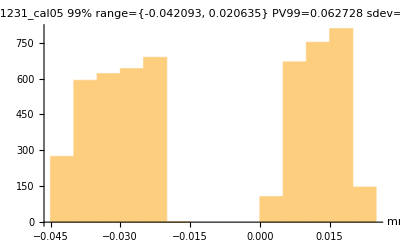

```mathematica
{histresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

Now fit a plane surface to the FID points

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
cFID[x_,y_]=Fit[FIDdata,fitbasisR,{x,y}]
```

0.00451836-0.000559859 x+0.00012068 y

```mathematica
vp1=vp
```

{1.26974,-1.4064,0.640157}

```mathematica
refplt=Plot3D[cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->200,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]]
```

-Graphics3D-

```mathematica
FIDcorrected=Table[{FIDdata[[i,1]],FIDdata[[i,2]],FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]}
,{i,1,Length[FIDdata]}
];
```

```mathematica
reflen$=ToString[Length[FIDcorrected]]
```

5307

```mathematica
FIDresidsPlt=ListPointPlot3D[FIDcorrected,PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"Xval","Yval","Z[µm]"},PlotLabel->fileinS<>"\nThis shows FID after subt plane fit"]
```

-Graphics3D-

```mathematica
Button["Export FIDresids plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDresids.tiff",FIDresidsPlt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Export FIDresids plot

```mathematica
zFIDresids=Take[FIDcorrected,All,{3}]//Flatten;
```

Look at quality of FID plane correction to FID points:

```mathematica
maxzR2=Max[zFIDresids];minzR2=Min[zFIDresids];sigmaR2=StandardDeviation[zFIDresids];
zbinR2=BinCounts[zFIDresids,(maxzR2-minzR2)/25];
hrange[binlist_,min_,max_]:=Quantile[binlist,{min,max}];
hgtrange99=hrange[zFIDresids,0.005,0.995];
PVrange99=hgtrange99[[2]]-hgtrange99[[1]];
sigmaR2//NumberForm[#,5]&
```

0.00060101

```mathematica
histFIDresidplt=Histogram[zFIDresids,50,ImageSize->400,BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],AxesLabel->{zunit$,""},PlotLabel->fileinS<>" FIDresids"<>"\n99%="<>ToString[hrange[zFIDresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$];
```

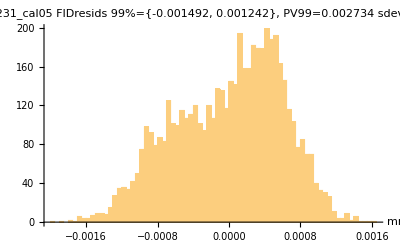

```mathematica
{histFIDresidplt,Dynamic[MousePosition["Graphics"]]}
```

```mathematica
Button["Export FID resids histogram plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDhist.tiff",histFIDresidplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID resids histogram plot

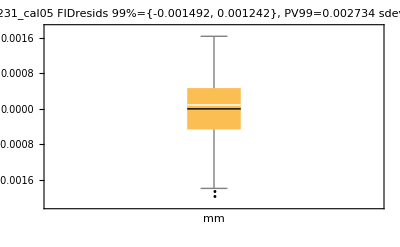

```mathematica
rbwc=BoxWhiskerChart[zFIDresids,{"Outliers",{"MeanMarker",1.0,Thick}},BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],PlotLabel->fileinS<>" FIDresids"<>"\n99%="<>ToString[hrange[zFIDresids,0.005,0.995]//NumberForm[#,4]&]<>", PV99="<>ToString[PVrange99//NumberForm[#,4]&]<>"\nsdev="<>ToString[sigmaR2//NumberForm[#,4]&]<>zunit$,AxesLabel->{zunit$,""}]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
Button["Export FID box whisker chart file",Export[ToString[StringDrop[fileinS,0]]<>"_"<>reflen$<>"_FIDboxwhisk.tiff",rbwc,"ImageEncoding"->"LZW",ImageResolution->100]]
```

Export FID box whisker chart file

```mathematica
vp1={2,0,0}
```

{2,0,0}

## 5. Now work on 3 ball fits.

#### Separate the regions and plot the points first.

First, separate the 3 ball region from the FID region. Use the y coords.

```mathematica
ballsOGPMM
```

{{14.3726,41.5273,-29.4012,4.00253},{100.879,41.6226,-29.3704,3.92891},{57.4938,155.055,-29.5195,4.13259}}

```mathematica
ballregions=Table[ Ball[Drop[ballsOGPMM,None,-1][[i]],4.5],{i,3}]
```

{Ball[{14.3726,41.5273,-29.4012},4.5],Ball[{100.879,41.6226,-29.3704},4.5],Ball[{57.4938,155.055,-29.5195},4.5]}

```mathematica
centregions=Table[ Ball[Drop[ballsOGPMM,None,-1][[i]],2.0],{i,3}]
```

{Ball[{14.3726,41.5273,-29.4012},2.],Ball[{100.879,41.6226,-29.3704},2.],Ball[{57.4938,155.055,-29.5195},2.]}

Separate data into regions for around each ball. blist contains the 3 region lists. Exclude the center point of the ball.

```mathematica
Do[If[i==1,blist={}];
templist={};
Do[
If[RegionMember[ballregions[[i]],cloudXYZ[[j]]]&& !RegionMember[centregions[[i]],cloudXYZ[[j]]],AppendTo[templist,cloudXYZ[[j]]],Null]
,{j,Length[cloudXYZ]}
];
Print[templist//Short];
AppendTo[blist,templist]
,{i,3}]
```

{{14.3738,41.5032,-25.3942},«722»,{14.6559,40.9144,-25.455}}

{{100.866,41.5898,-25.4346},«501»,{103.246,42.4016,-26.4328}}

{{57.5679,155.039,-25.392},«362»,{58.7848,154.68,-25.601}}

```mathematica
blist//Short
```

{{{14.3738,41.5032,-25.3942},«722»,{14.6559,40.9144,-25.455}},{«1»},{«1»}}

```mathematica
Length[blist[[1]]]
```

724

```mathematica
testS=.;testR=.;SUTdata=.;FIDdata=.;
```

```mathematica
ballplot[balldata_,ballID$_]:=ListPointPlot3D[balldata,PlotRange->All,ViewPoint->{0,-3,1},ColorFunction->"Rainbow",ImageSize->400,AxesLabel->{"X[mm]","Y[mm]","Z[mm]"},PlotLabel->"Ball "<>ballID$]
```

```mathematica
bplt={};
```

```mathematica
bplt=Table[ballplot[blist[[i]],ToString[i]],{i,1,3}];
```

```mathematica
allBallptsplot=GraphicsRow[bplt,ImageSize->600]
```

-Graphics-

```mathematica
Button["Output ball point cloud plot",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_Ballpts.tiff",allBallptsplot,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output ball point cloud plot

#### Now fit each ball to a sphere and extract the coords.

Fist, express z as a function of the 4 parameters. Solve the canonical equation for z.

```mathematica
RR=.;x0=.;y0=.;z0=.;r0=.;
```

```mathematica
spheqn=(x-x0)^2+(y-y0)^2+(z-z0)^2-r0^2==0
```

-r0^2+(x-x0)^2+(y-y0)^2+(z-z0)^2==0

```mathematica
solnz=Solve[spheqn,z]
```

{{z→-√(r0^2-x^2+2 x x0-x0^2-y^2+2 y y0-y0^2)+z0},{z→√(r0^2-x^2+2 x x0-x0^2-y^2+2 y y0-y0^2)+z0}}

```mathematica
eqnz=z/.solnz[[2]]
```

√(r0^2-x^2+2 x x0-x0^2-y^2+2 y y0-y0^2)+z0

Function to fit to a ball data input array

```mathematica
nominalR=4.0; (*Need initial guess*)
```

```mathematica
fitballdata[ptclouddata_]:= 
Block[{pts},pts=ptclouddata;pts0=Mean[pts];fitpts=NonlinearModelFit[pts,eqnz,{{x0,pts0[[1]]},{y0,pts0[[2]]},{z0,pts0[[3]]},{r0,nominalR}},{x,y}];fitpts[{"BestFitParameters","ParameterConfidenceIntervalTable"}]//Column]
```

```mathematica
fitballdata[blist[[3]]]
```

{x0→57.558,y0→155.066,z0→-29.4029,r0→4.01039}
 | Estimate | Standard Error | Confidence Interval
x0 | 57.558 | 0.000632475 | {57.5567,57.5592}
y0 | 155.066 | 0.000683388 | {155.065,155.067}
z0 | -29.4029 | 0.00171085 | {-29.4062,-29.3995}
r0 | 4.01039 | 0.00146605 | {4.00751,4.01327}

```mathematica
fitpts["FitResiduals"]//Short
```

{0.000542919,«362»,0.00321516}

```mathematica
Do[If[i==1,fitpts=.;fitres1={};fitres2={};fitres3={};fitfcn={};pts0={};fitzresids={};ballfits={}];


pts0=Mean[blist[[i]]];(*Print[pts0];*)fitpts=NonlinearModelFit[blist[[i]],eqnz,{{x0,pts0[[1]]},{y0,pts0[[2]]},{z0,pts0[[3]]},{r0,nominalR}},{x,y}];
AppendTo[ballfits,{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}]];{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}];
Print[{x0,y0,z0,r0}/.fitpts[{"BestFitParameters"}]];
AppendTo[fitzresids,fitpts[{"FitResiduals"}]];AppendTo[fitfcn,fitpts[{"BestFit"}]];
AppendTo[fitres1,fitpts[{"BestFitParameters"}]];AppendTo[fitres2,fitpts[{"ParameterConfidenceIntervalTable"}]];AppendTo[fitres3,fitpts[{"ANOVATable"}]]

,{i,3}]
```

{{14.3681,41.5232,-29.4031,4.00571}}

{{100.848,41.6217,-29.439,4.00313}}

{{57.558,155.066,-29.4029,4.01039}}

```mathematica
ballfits=Flatten[ballfits,1]
```

{{14.3681,41.5232,-29.4031,4.00571},{100.848,41.6217,-29.439,4.00313},{57.558,155.066,-29.4029,4.01039}}

```mathematica
fitzresids=Flatten[fitzresids,1];(*Get rid of extra level*)
```

```mathematica
out$=fileinS<>"\nParameters are {x0,y0,z0,r0}\nNominal OGP values: \n"<>ToString[ballsOGPMM//Column]<>"\n\nFit parameters:\n";
```

```mathematica
{out$,fitres1//Column,fitres2//Column};
```

```mathematica
Button["Output the fit results to PDF",Export[StringTake[fileinS,12]<>"BallFits3.PDF",{out$,fitres1//Column,fitres2//Column}//Column]]
```

Output the fit results to PDF

Look at histogram of residuals of each ball after subtracting best fit sphere. Look for particularly bad fits and then figure out why.

```mathematica
sdev=Map[StandardDeviation,fitzresids]
```

{0.00379792,0.00843148,0.00471665}

```mathematica
kurt=Map[Kurtosis,fitzresids]
```

{6.68625,105.061,6.48908}

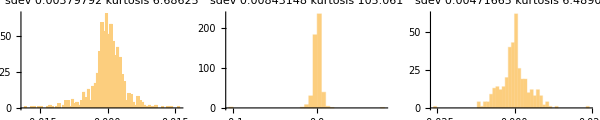

```mathematica
histoplt=GraphicsRow[Table[Histogram[fitzresids[[i]],50,BaseStyle->Directive[FontSize->6,FontFamily->"Arial"],PlotLabel->"sdev "<>TS[sdev[[i]]]<>"\nkurtosis "<>TS[kurt[[i]]]],{i,Length[fitzresids]}],ImageSize->600]
```

```mathematica
Button["Output pt residual histograms",Export[ToString[StringDrop[fileinS,0]]<>"_"<>"_3zreshisto.tiff",histoplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output pt residual histograms

Compute the difference between the MeasureMind coords and the Mathematica fits to the point clouds. Export the points and the differences to an Excel file.

```mathematica
ballfits
```

{{14.3681,41.5232,-29.4031,4.00571},{100.848,41.6217,-29.439,4.00313},{57.558,155.066,-29.4029,4.01039}}

```mathematica
ballsOGPMM
```

{{14.3726,41.5273,-29.4012,4.00253},{100.879,41.6226,-29.3704,3.92891},{57.4938,155.055,-29.5195,4.13259}}

```mathematica
ballcoorddiffs=ballfits-ballsOGPMM
```

{{-0.0045351,-0.00413505,-0.00190093,0.00318198},{-0.0317677,-0.00084228,-0.0685582,0.0742232},{0.0641577,0.0114822,0.116686,-0.122199}}

Format the results for output to Excel file.

```mathematica
ballsOGPout=Prepend[ballsOGPMM,{"x0","y0","z0","r0"}];
ballsOGPout=Prepend[Transpose[ballsOGPout],{"MMfits","LL","LR","UC"}];
ballsOGPout=Prepend[ballsOGPout,{fileinS<>"\nMeasureMind fit results","","",""}];
```

```mathematica
ballfitsout=Prepend[ballfits,{"x0","y0","z0","r0"}];ballfitsout=Prepend[Transpose[ballfitsout],{"SurfCalc fits","LL","LR","UC"}];ballfitsout= Prepend[ballfitsout,{fileinS<>"\nSurfCalc fits to point clouds","","",""}];
```

```mathematica
ballcoorddiffsout=Prepend[ballcoorddiffs,{"x0","y0","z0","r0"}];
ballcoorddiffsout=Prepend[Transpose[ballcoorddiffsout],{"Difference SurfCalc-MM","LL","LR","UC"}];
ballcoorddiffsout=Prepend[ballcoorddiffsout,{fileinS<>"\nDifference: SurfCalc - MeasureMind","","",""}];
```

```mathematica
Button["Output the ballcoorddiffs results",
Export[StringTake[fileinS,12]<>"BallFits3.xls",{ballsOGPout,ballfitsout,ballcoorddiffsout}]]
```

Output the ballcoorddiffs results

#### Plot results

```mathematica
vp1={0,-2,2.0};
```

Define a plot function that will plot any one of the surface fits. Take the center points from the fit centers in fitres1 and set the plot region size with the delta parameter. The ReleaseHold and Hold and Evaluate is necessary to allow the plot range limits to be calculated before the plot is evaluated.

```mathematica
Bfitplt=.;
```

```mathematica
Bfitplt[i_,delta_]:=ReleaseHold@(Hold[Plot3D[fitfcn[[i]],Evaluate[{x,x0-delta,x0+delta}],Evaluate[{y,y0-delta,y0+delta}],ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.3],ViewPoint->Dynamic[vp1]]]//.fitres1[[i,1]])
```

```mathematica
BallandFit[i_]:=Show[Bfitplt[i,3],bplt[[i]],PlotRange->All,ViewPoint->Dynamic[vp1],AxesLabel->{"X[mm]","Y[mm]",""},PlotLabel->fileinS<>"\nSpherical fit to OGP ball points"]
```

```mathematica
BallFitsPts=GraphicsRow[Table[BallandFit[i],{i,3}],ImageSize->600]
```

-Graphics-

```mathematica
Button["Output points and fit graphics",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_Ballpts.tiff",BallFitsPts,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output points and fit graphics

```mathematica
Dynamic[vp1]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

#### Plot FID surface fit with ball fit surfaces.

```mathematica
refplt=Plot3D[cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->200,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1]];
```

```mathematica
Show[refplt,BallandFit[1],BallandFit[2],BallandFit[3],PlotRange->All,ImageSize->400,ViewPoint->Dynamic[vp1],AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

Now compute the distance of the ball centers from the Ref plane at the ball xy centers. Ball centers define datum plane. First compute datum plane equation from ball centers. THen plot the difference between the 2 planes.

```mathematica
fitbasisR={1,x,y};fitidxR="1,1";
fitordR$=StringTake[ToString[fitbasisR],{2,-2}]
```

1, x, y

```mathematica
cDATUM[x_,y_]=balldatumplaneOGP[x,y]
```

-29.3574+0.00035757 x-0.00117803 y

```mathematica
Datumplt=Plot3D[cDATUM[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.5],ViewPoint->Dynamic[vp1],AxesLabel->{"X","Y","Z"},PlotLabel->fileinS<>"\ncDATUM plane"]
```

-Graphics3D-

```mathematica
Button["Output cDATUM plot",Export[ToString[StringDrop[fileinS,0]]<>"_cDATUM.tiff",Datumplt,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output cDATUM plot

```mathematica
ptsanddatums=Show[lpp01,Datumplt,refplt,PlotLabel->fileinS<>"\nPts & Fit planes",PlotRange->All]
```

-Graphics3D-

```mathematica
Button["Output points and fit planes",Export[ToString[StringDrop[fileinS,0]]<>"_"<>fitidx<>"_"<>hms$<>"_pts&fitplanes.tiff",ptsanddatums,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output points and fit planes

```mathematica
cDATUMFIDdiff[x_,y_]=cDATUM[x,y]-cFID[x,y]
```

-29.362+0.00091743 x-0.00129871 y

```mathematica
(cDATUM[x,y]-cFID[x,y])/.x->50/.y->100
```

-29.446

```mathematica
Button["Output the equation results",
Export[StringTake[fileinS,12]<>"planeeqns.txt",{fileinS<>"\ncDatum[x,y]= "<>ToString[cDATUM[x,y]]<>"\ncFID[x,y] = "<>ToString[cFID[x,y]]<>"\ncDATUM-cFID = "<>ToString[cDATUMFIDdiff[x,y]]}]]
```

Output the equation results

```mathematica
Plot3D[cDATUM[x,y]-cFID[x,y],{x,xminBalls,xmaxBalls},{y,ymin,ymax},ColorFunction->"Rainbow",ImageSize->400,PlotStyle->Opacity[0.9],AxesLabel->{"Xval","Yval",""},ViewPoint->Dynamic[vp1],PlotLabel->"Difference between Datum and Fiducial planes"]
```

-Graphics3D-

This shows the FID surface, defined by the fiducial flats on the fixture, relative to the datum surface defined by the 3 ball centers. The actual raft surface needs to be 29.81mm above the datum plane. One can see that the fiducial plane is offset and tilted from the nominal raft surface plane. We want to be able to use the fiducial surfaces as a proxy for the 3 ball centers, as that is what is only visible during the raft measurement. NOTE that these points and planes are measured in the OGP machine global coord system, not referenced to a point on the fixture. The nominal points on the raft surface can be set from the measured ball centers, then a plane fit to those points. The difference between that plane and the observed fiducial plane is the correction that needs to be added to the fiducial plane. Make sure the coord system doesn’t change, as the expression for the planes depends upon the location of the origin.

```mathematica
nomRaftPts=Map[Apply[Plus,{#,{0,0,29.81}}]&,Drop[ballsOGPMM,None,-1]] (*Add the nom raft height value to the z-coords*)
```

{{14.3726,41.5273,0.40878},{100.879,41.6226,0.4396},{57.4938,155.055,0.29046}}

```mathematica
nomRaftSurfFit[x_,y_]=Fit[nomRaftPts,{1,x,y},{x,y}]
```

0.452561+0.00035757 x-0.00117803 y

DATUM is the surface fit to the 3 ball centers.
FID is the surface fit to the 2 reference flats.
   The coordinate system X,Y origin for all measurements is the global OGP system initialization coordinates. The Z origin is on the top surface of the front fiducial at a specific x,y location.
   The DATUM and FID surfaces are measured during the calibration runs. The plane fit equations to these surfaces are used during the measurement of the raft surface. Need to check to see how repeatable the fit equations are between calibration runs when no changes are made to the location of the fixtures. The raft measurement depends on the calibration surfaces remaining unchanged.
	(cDATUM - cFID) = constant over time.
This difference references the datum surface to the fiducial surface.
   Now measure the raft and the fiducial surface:
	(mRaft - mFID) is the raft surface referenced to the fiducial surface.
   Taking the difference:
	(mRaft - mFID) - (cDATUM - cFID) = mRaft - cDATUM
because this assumes that the fiducial surface fits are the same.
    This last expression defines the absolute raft height relative to the datum plane. The nominal height of the raft above the datum is 29.81mm, so this number can be subtracted from the absolute height to get the residual absolute height error of the raft from the nominal surface plane.

## 6. Lateral ball position distances.

Extract the x,y positons from the ball centers. Compute the distance between the 2 lower balls and the distance from the midpoint between them to the upper ball.

```mathematica
ballsMMxy=Drop[ballsOGPMM,None,-2]
```

{{14.3726,41.5273},{100.879,41.6226},{57.4938,155.055}}

```mathematica
MMxdistLLLR=Norm[ballsMMxy[[1]]-ballsMMxy[[2]]];
xmid=(ballsMMxy[[2]]-ballsMMxy[[1]])[[1]]/2;
ymid=(ballsMMxy[[2]]+ballsMMxy[[1]])[[2]]/2;
MMydistUCmid=Norm[ballsMMxy[[3,2]]-{xmid,ymid}[[2]]];
```

```mathematica
Print["MM locs: X dist (86.50) = ",MMxdistLLLR,", Y dist (113.50) = ",MMydistUCmid]
```

MM locs: X dist (86.50) = 86.5067, Y dist (113.50) = 113.48

```mathematica
ballsfitxy=Drop[ballfits,None,-2]
```

{{14.3673,41.5225},{100.858,41.6236},{57.5557,155.064}}

```mathematica
SCxdistLLLR=Norm[ballsfitxy[[1]]-ballsfitxy[[2]]];
xmid=(ballsfitxy[[2]]-ballsfitxy[[1]])[[1]]/2;
ymid=(ballsfitxy[[2]]+ballsfitxy[[1]])[[2]]/2;
SCydistUCmid=Norm[ballsfitxy[[3,2]]-{xmid,ymid}[[2]]];
```

```mathematica
Print["SurfCalc locs: X dist (86.50) = ",MMxdistLLLR,", Y dist (113.50) = ",SCydistUCmid]
```

SurfCalc locs: X dist (86.50) = 86.5067, Y dist (113.50) = 113.491

```mathematica
Button["Output lateral ball separations",
Export[StringTake[fileinS,12]<>"_ballseps.txt",
{fileinS<>"\nMM dist: X dist (86.50) = "<>TS[MMxdistLLLR]<>", Y dist (113.50) = "<>TS[MMydistUCmid]<>"\nSurfCalc dist: X dist (86.50) = "<>TS[MMxdistLLLR]<>", Y dist (113.50) = "<>TS[SCydistUCmid]}]]
```

Output lateral ball separations

## 7. Compare cDATUM - cFID plane equations.

Reference the datum plane to the fiducial plane and look at the difference between different runs. Each run consists of switching off the OGP machine, exiting MeasureMind, then restarting the machine and MeasureMind, which causes the OGP to seek home on each axis. Then find and set the SCS origin at the center of the crossed scribe marks. THen run the ball and fiducial surface routine and do the plane fitting above. Reference the datum surface to the FID plane by taking the difference, then compare these difference equations to see how repeatable this process is.

```mathematica
eqn={};
```

```mathematica
eqn1=-29.3574+0.00035757 x-0.00117803 y;
eqn2=-29.3619+0.000914132 x-0.00130154 y;
eqn3=-29.362+0.000917461 x-0.00129783 y;
eqn4=-29.3625+0.000911063 x-0.00130114 y;
eqn5=-29.3619+0.000917168 x-0.00129874 y;
```

```mathematica
eqn={eqn1,eqn2,eqn3,eqn4,eqn5}
```

{-29.3574+0.00035757 x-0.00117803 y,-29.3619+0.000914132 x-0.00130154 y,-29.362+0.000917461 x-0.00129783 y,-29.3625+0.000911063 x-0.00130114 y,-29.3619+0.000917168 x-0.00129874 y}

```mathematica
eqn2-eqn1/.x->10/.y->10
```

-0.00016948

```mathematica
datumplanestability=GraphicsGrid[Table[Plot3D[eqn[[i]]-eqn[[j]],{x,xminBalls,xmaxBalls},{y,ymin,ymax},PlotLabel->"{i,j}="<>TS[i]<>","<>TS[j],BaseStyle->Directive[FontSize->8,FontFamily->"Arial"]],{i,Length[eqn],1,-1},{j,i-1,1,-1}],ImageSize->800,BaseStyle->Directive[FontSize->12,FontFamily->"Arial"]]
```

-Graphics-

```mathematica
Button["Output datum plane stability plot",Export[ToString[StringDrop[fileinS,0]]<>"_datumStabil.tiff",datumplanestability,"ImageEncoding"->"LZW",ImageResolution->100],Method->"Queued"]
```

Output datum plane stability plot

```mathematica
{x,xminBalls,xmaxBalls},{y,ymin,ymax}
```

## Plot combined DistributionChart for several height residual data files.

#### Default directory is same as set earlier.

First list the desired XLSX files using the wild card. THen edit the picklist to select the desired files. THe result is

```mathematica
upstemoffset=4.49;
```

```mathematica
Input["Enter upstem offset value that gets subtracted from the input height data. This must correspond to the value measured during the initial calibration run on the day of the measurements.",upstemoffset]
```

```mathematica
fnames1=FileNames["*SUTcorrAbsHgt.xlsx"]
```

```mathematica
Table[{i,fnames1[[i]]},{i,Length[fnames1]}]//TableForm
```

Create picklist here:

```mathematica
picklist={1,2,4,5,7,8};
```

```mathematica
picklist={1,2,4,5,6,7,8,9,10,11}
```

```mathematica
data2=Table[Drop[(Import[fnames1[[i]],"Data"][[1,All,{3}]]//Flatten)-upstemoffset,1]
,{i,picklist}];
```

```mathematica
Dimensions[data2[[]]]
```

```mathematica
Short[data2,10]
```

Now generate qlist with 2 significant digits. Then convert to strings and replace the comma separators with newlines within each row. This preserves the list structure but makes the string list print out vertically to use as annotation for the x-axis.

```mathematica
quantlist=Reverse[{0.0,0.005,0.025,0.50,0.975,0.995,1.0}];
```

```mathematica
qlist=Map[Quantile[#,quantlist]&,data2]
```

```mathematica
qrows=Map[NumberForm[#,{4,2}]&,qlist]
```

```mathematica
qrows2=Map[StringReplace[ToString[#],{","->"\n","{"->"","}"->""}]&,qrows];
```

```mathematica
Dimensions[qrows2]
```

Compute list of median values.

```mathematica
medlist=Map[NumberForm[Median[#],3]&,data2]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
combinedplt=DistributionChart[data2,ChartLabels->Placed[{medlist,qrows2},{Center,Axis}],BaseStyle->Directive[Bold,FontFamily->"Arial",FontSize->12],FrameLabel->{"",zunit$},AxesLabel->{zunit$,zunit$},ImageSize->500,PlotLabel->"Absolute height relative to 13.000mm\nCorrected for upstem offset of "<>ToString[upstemoffset]<>zunit$]
```

Keep existing value for plot neame if it already exists. Otherwise, set it to a default NoName.

```mathematica
If[ValueQ[comboplt],Null,comboplt="NoName"]
```

```mathematica
comboplt=InputString["Enter file name for output of the plot file.",comboplt]
```

```mathematica
Button["Export combined result plot",Export[comboplt<>"_comboDensityPlot.tiff",combinedplt,"ImageEncoding"->"LZW",ImageResolution->100]]
```

## Removed from above

```mathematica
stepinc=1;
imin=xmin;imax=xmax;jmin=ymin;jmax=ymax;
manualcalcFlag
```

```mathematica
If[manualcalcFlag,MessageDialog["Set SUT and FID regions with sliders after ABORT"],jmin=-5;jmax=45;MessageDialog["Automatic selection of CCD and gauge block regions"]]  
(*for automated analysis*)  (*Fixed values for CCD and gauge blocks on upstems. Bypass the Manipulate*)
```

Isolate the CCD region. THis will define the inclusion limits in Y-dir for dividing the data into FID and SUT regions.

```mathematica
Manipulate[Show[lpp01,ImageSize->300,ViewPoint->Dynamic[vp],PlotRange->{{imin,imax},{jmin,jmax},All}]
,{{imin,xmin,"xmin"},xmin,imax,stepinc,Appearance->"Open"},{{imax,xmax,"xmax"},imin,xmax,stepinc,Appearance->"Open"}
,{{jmin,ymin,"ymin"},ymin,jmax,stepinc,Appearance->"Open"},{{jmax,ymax,"ymax"},jmin,ymax,stepinc,Appearance->"Open"},LocalizeVariables->False,SynchronousInitialization->False,SynchronousUpdating->False]
```

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
If[manualcalcFlag,Input["Abort and set sliders now to isolate CCD surface region, then execute next section."]]
```

#### Solve spherical fit according to book.

Start with test data.

```mathematica
rt=4.;pt={};
```

```mathematica
Do[xt=RandomReal[{-rt,rt}];
yt=RandomReal[{-Sqrt[rt^2-xt^2],Sqrt[rt^2-xt^2]}];
zt=RandomReal[0.1]+Sqrt[Abs[rt^2-(xt^2 +yt^2 )]];
AppendTo[pt,{xt,yt,zt}],{i,1,10}]
```

```mathematica
pt
```

{{3.65784,1.10867,1.19277},{-3.53811,1.50084,1.14812},{-3.8349,-0.728613,0.878458},{3.16347,-0.935747,2.30807},{2.04878,-0.272406,3.5005},{2.88927,-0.291662,2.75299},{3.58612,1.54383,0.954597},{2.58202,-1.54018,2.66162},{-3.61727,1.54328,0.770985},{-3.85332,0.663812,0.893803}}

```mathematica
ballplot[pt,""]
```

-Graphics3D-

```mathematica
Transpose[2 pt]
```

{{7.31567,-7.07622,-7.66981,6.32695,4.09755,5.77855,7.17224,5.16403,-7.23453,-7.70663},{2.21733,3.00169,-1.45723,-1.87149,-0.544811,-0.583324,3.08767,-3.08037,3.08655,1.32762},{2.38553,2.29624,1.75692,4.61614,7.00099,5.50597,1.90919,5.32325,1.54197,1.78761}}

```mathematica
ones=ConstantArray[-1,Length[pt]]
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Head[ones]
```

List

```mathematica
Amat=Append[Transpose[2 pt],ones]//Transpose
```

{{7.31567,2.21733,2.38553,-1},{-7.07622,3.00169,2.29624,-1},{-7.66981,-1.45723,1.75692,-1},{6.32695,-1.87149,4.61614,-1},{4.09755,-0.544811,7.00099,-1},{5.77855,-0.583324,5.50597,-1},{7.17224,3.08767,1.90919,-1},{5.16403,-3.08037,5.32325,-1},{-7.23453,3.08655,1.54197,-1},{-7.70663,1.32762,1.78761,-1}}

```mathematica
Bmat=Apply[Plus,pt^2,1]
```

{16.0316,16.0889,16.0091,16.2104,16.5252,16.0119,16.1549,16.1232,16.0607,16.0876}

This is initial guess:

```mathematica
{xc0,yc0,zc0,rho}=LinearSolve[Transpose[Amat]. Amat,Transpose[Amat] .Bmat]
```

{-0.00361395,0.0274591,0.0773573,-15.8544}

```mathematica
rsqrt=xc0^2 +yc0^2 +zc0^2 -rho^2//Abs//Sqrt
```

15.8542

```mathematica
Sqrt[rsq]
```

0.+15.8542 ⅈ

```mathematica
Rfcn[ipt_,pt_List]:=Sqrt[(pt[[ipt,1]]^2-xc0)^2+(pt[[ipt,2]]^2-yc0)^2+(pt[[ipt,3]]^2-zc0)^2]
```

```mathematica
Rfcn[3,pt]
```

14.7351

```mathematica
Jmat=Table[-(pt[[j,i]]-xc0)/Rfcn[j,pt]
,{j,1,Length[pt]},{i,1,3}
]
```

{{-0.27113,-0.0823641,-0.0885919},{0.2766,-0.117735,-0.0901317},{0.260011,0.0492022,-0.059862},{-0.279384,0.082228,-0.203925},{-0.15934,0.020868,-0.272046},{-0.257694,0.0256589,-0.245553},{-0.273934,-0.118086,-0.0731213},{-0.259749,0.154362,-0.267747},{0.271533,-0.116235,-0.0582041},{0.258805,-0.0448692,-0.0603309}}

```mathematica
Jmat=Append[Transpose[Jmat],ones]//Transpose
```

{{-0.27113,-0.0823641,-0.0885919,-1},{0.2766,-0.117735,-0.0901317,-1},{0.260011,0.0492022,-0.059862,-1},{-0.279384,0.082228,-0.203925,-1},{-0.15934,0.020868,-0.272046,-1},{-0.257694,0.0256589,-0.245553,-1},{-0.273934,-0.118086,-0.0731213,-1},{-0.259749,0.154362,-0.267747,-1},{0.271533,-0.116235,-0.0582041,-1},{0.258805,-0.0448692,-0.0603309,-1}}

```mathematica
Dmat=Table[(Rfcn[i,pt]-rsqrt)^2,{i,1,Length[pt]}]
```

{5.52132,9.4605,1.25233,20.4142,8.84222,21.4192,7.56119,34.8079,6.48129,0.958913}

```mathematica
LinearSolve[Transpose[Jmat].Jmat,-Transpose[Jmat].Dmat]
```

{7.68098,-32.4342,51.327,4.52909}

#### Iterate FID trim and fit, if necessary.

Trim off bad points from FID region.

Trim the outliers here.

```mathematica
SelectionMove[nb,After,GeneratedCell]
```

```mathematica
threshR=sigmaR2*4
```

```mathematica
threshR=Input["Enter ±threshold value for trimming bad FID points.",threshR]
```

Trim both the XYZ and the Z data lists

```mathematica
(* Remove the plane from the z-data but not from the XYZ data*)FIDresidsZtrim=Drop[Reap[ Do[If[Abs[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]<threshR,Sow[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]],{i,Length[FIDdata]}]],1]//Flatten[#,2]&;
```

```mathematica
FIDdatatrim=Drop[Reap[ Do[If[Abs[FIDdata[[i,3]]-cFID[FIDdata[[i,1]],FIDdata[[i,2]]]]<threshR,Sow[FIDdata[[i]]]],{i,Length[FIDdata]}]],1]//Flatten[#,2]&;
```

```mathematica
FIDresidsXYZtrim=Table[{FIDdatatrim[[i,1]],FIDdatatrim[[i,2]],FIDresidsZtrim[[i]]},{i,Length[FIDdatatrim]}];
```

```mathematica
refflag=0;
refflag=Input["If need to iterate FID fit, set refflag to 1",refflag]
If[refflag==1,FIDdata=FIDdatatrim;NotebookLocate["FIDdata iterate restart"];Abort[],MessageDialog["Finished with FID"]]
```